## 2. domača naloga (5. vaje)

## 1. naloga

V Mathematici predstavimo daljico v obliki Daljica[AA_, BB_], kjer sta AA in BB točki predstavljeni s parom koordinat v obliki {x, y}. 

Primer: d = Daljica[{-1, 1}, {3, -1}].

Sestavi naslednje funkcije :

Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice.

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

Slika[Daljica[AA_, BB_]], ki vrne grafični objekt Line, kateri predstavlja daljico.

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

Narisi[d__Daljica], ki za eno ali več podanih daljic le - te izriše.

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

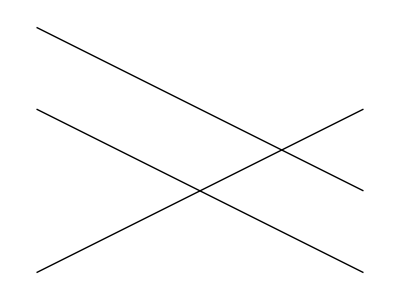

```mathematica
Narisi[d, d2, d3]
```

EnacbaNosilke[Daljica[AA_, BB_]], ki rne enačbo premice nosilke daljice. Primer, za daljico d kot zgoraj je enačba nosilke y == -x/2 + 1/2

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

## 2. naloga

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

Presek[Daljica[{-1,1},{3,-1}],Daljica[{-1,-1},{3,1}]]

```mathematica
Presek[d, d3]
```

Presek[Daljica[{-1,1},{3,-1}],Daljica[{-1,2},{3,0}]]

## 3. naloga

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik. 

Primer: m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}].

Gre za sklenjen mnogokotnik, zato predvidevamo, da ima ta povezave med zaporednimi točkami ter od zadnje do prve točke. 


Sestavi naslednje funkcije :

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
m2 =Append[m1,m1[[1]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

Slika(Mnogokotnika):

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
Slika[m2]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

Narisi(m- mnogokotnik):

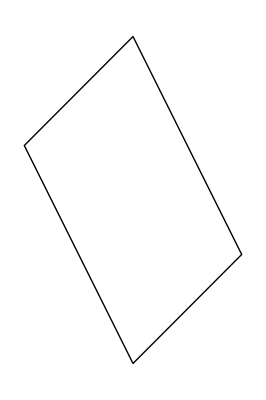

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Slika[m]]
Narisi[m2]
```

PravilniNKotnik:

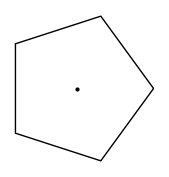

```mathematica
PravilniNKotnik[n_,r_] :=Graphics[{Line[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5 = PravilniNKotnik[5,2]
```

Brez uporabe dodane formule:

```mathematica
PravilniNKotnik2[n_,r_] := Show[Graphics[{{EdgeForm[Thick],White,RegularPolygon[{0,0},r,n]},{Point[{0,0}]}}]]
p55=PravilniNKotnik2[5,2]
```

-Graphics-

Nadgradi prejšnjo funkcijo v PravilniNKotnik :

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
pNeki = Manipulate[PravilniNKotnik[5,2,phi],{phi,1.5,33}]
```

Daljice(Mnogokotnika) :

Oglej si, kaj naredita naslednja ukaza : 
	Partition[{1, 2, 3, 4, 5}, 2]
	Partition[{1, 2, 3, 4, 5}, 2, 1]

```mathematica
Daljice[Mnogokotnik[t__]] := Map[Daljica,Partition[{t}, 2,1]]
daljice = Daljice[m2]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

```mathematica
Partition[{1,2,3,4,5},2]
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

## 4. naloga

Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in daljice.

```mathematica
Presek2[m_Mnogokotnik,d_Daljica] := Presek[daljice[[1]],d]
Presek2[m2,d]
daljice[[1]]
```

Presek[Daljica[{{0,0},{1,1}}],Daljica[{-1,1},{3,-1}]]

Daljica[{{0,0},{1,1}}]

## 5. naloga

Spodnja funkcija izračuna (uporabi) funkcijo f na vseh parih iz dveh seznamov.

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
```

```mathematica
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Outer[f,{1,2,3},{4,5,6}]
```

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

```mathematica
Flatten[{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}},1]
```

{f[1,4],f[1,5],f[1,6],f[2,4],f[2,5],f[2,6],f[3,4],f[3,5],f[3,6]}

```mathematica
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
```

```mathematica
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[g,m1,m2]
```

## 6. naloga

Napiši enačbo premice, ki vsebuje A(1, 2, 3) in je vzporedna vektorju (1, -1, 2) v parametrični in kanonični obliki.

Predpostavimo začetno točko 0 v prostoru in neko točko X, ki leži na premici.

```mathematica
OX = {0, x}
OA = {0, a} 
p = AX

OX = OA + AX = OA +( c * p)
{x,y ,z} = {1, 2, 3} + c * {1, -1, 2}
```

Parametrična oblika enačbe premice:

```mathematica
x = 1 + c
y = 2 - c
z = 3 + 2c
```

Kanonična oblika premice:

```mathematica
c = x- 1 = 2 - y = (z-3)/2
p = (x - 1) / 1 = (y - 2) / 1 = (z - 3) / 2
```